# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Kicked LMG

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);

Clear[F];
F[J_,α_,k_,τ_]:=MatrixExp[N[(-I*k/(2J))(Sx[J].Sx[J])]].MatrixExp[(-I*α*τ)(Sz[J])];

Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

## LMG

```mathematica
Clear[Hlmg, floq];
Hlmg[J_]:=Hlmg[J]=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
```

```mathematica
Clear[gx,gy];
J=300;
gx=-95/100;
gy=3gx;
```

```mathematica
Clear[lipmatm,lipmatM];
mat2=Hlmg[J];
(*mat2=ConjugateTranspose[rotation].Hlmg[J].rotation;*)
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

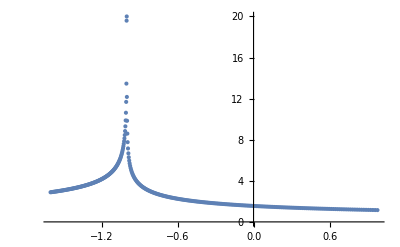

```mathematica
ListPlot[Transpose[{lipeigenvalM[[1;;-2]]/J,(2Pi)/Differences[Chop[lipeigenvalM]]}],PlotRange->All]
(*ListPlot[(2Pi)/Differences[Chop[lipeigenvalm]],PlotRange->All]*)
```

## Kicked LMG

```mathematica
Clear[floq];
floq[J_,gx_,gy_,ϵ_,tau_]:=N[MatrixExp[(-I*ϵ)(Sz[J])].MatrixExp[-I*tau*Hlmg[J]]];
```

```mathematica
tau=Chop[(2Pi)/(lipeigenvalM[[2]]-lipeigenvalM[[1]])]
epsilon=(-0.00001)(tau)
```

2.88472

-0.0000288472

```mathematica
Clear[mat];
mat=floq[J,gx,gy,epsilon,tau];
(*rotation=MatrixExp[I(N[Pi])Sx[J]];*)
(*mat=ConjugateTranspose[rotation].floq[J,gx,gy,epsilon,tau].rotation;*)
Clear[floqmatm,floqmatM];
floqmatM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
floqmatm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{floqeigenvalM,floqeigenvecM}=Eigensystem[floqmatM];
{floqeigenvalm,floqeigenvecm}=Eigensystem[floqmatm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
floqneweigenvecM=Table[Riffle[floqeigenvecM[[j]],zerosM],{j,J+1}];
floqneweigenvecm=Table[Riffle[zerosm,floqeigenvecm[[j]]],{j,J}];
floqneweigenvec=Riffle[floqneweigenvecM,floqneweigenvecm];
floqneweigenval=Riffle[floqeigenvalM,floqeigenvalm];
```

```mathematica
h0=ParallelTable[Chop[Conjugate[i].lipmatM.i],{i,floqeigenvecM}];
```

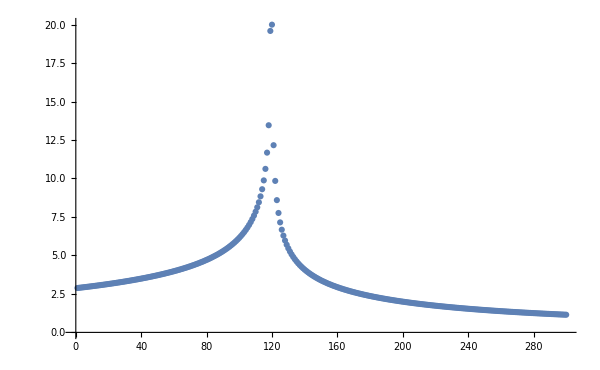

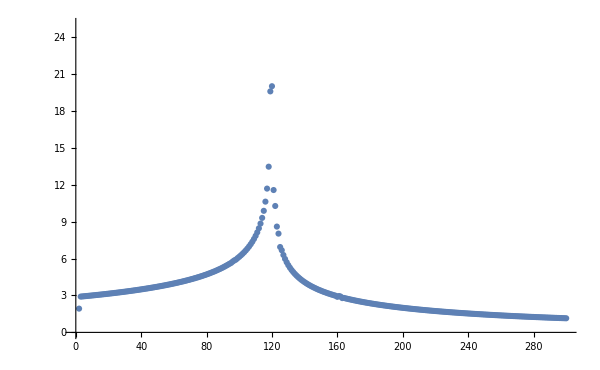

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All,ImageSize->600]
ListPlot[2Pi/Differences[Sort[h0]],ImageSize->600,PlotRange->{All,{0,25}}]
```

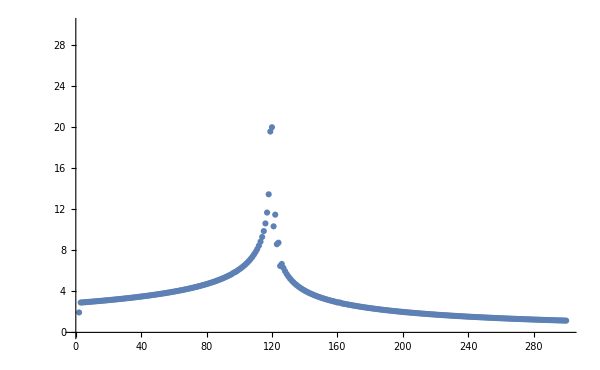

```mathematica
ListPlot[2Pi/Differences[Sort[h0]],ImageSize->600,PlotRange->{All,{0,30}}]
```

# <r>

```mathematica
Clear[Hlmg, floq];
Hlmg[J_,gx_,gy_]:=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
floq[J_,gx_,gy_,ϵ_,tau_]:=N[MatrixExp[(-I*ϵ)Sz[J]].MatrixExp[-I*tau*Hlmg[J,gx,gy]]];
```

```mathematica
Clear[gx,gy,epsilon];
gx=-5/10;
gy=-3/10;
tau=5.0;
J=200;
```

```mathematica
Clear[mat2,mat];
mat2=Hlmg[N[J],gx,gy];
Clear[lipmatm,lipmatM];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

```mathematica
2*Pi*lipneweigenval[[1]]/J
```

-6.28962

```mathematica
mat=floq[N[J],gx,gy,epsilon,tau];
Clear[floqmatm,floqmatM];
floqmatM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
floqmatm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{floqeigenvalM,floqeigenvecM}=Eigensystem[floqmatM];
{floqeigenvalm,floqeigenvecm}=Eigensystem[floqmatm];
floqneweigenvecM=Table[Riffle[floqeigenvecM[[j]],zerosM],{j,J+1}];
floqneweigenvecm=Table[Riffle[zerosm,floqeigenvecm[[j]]],{j,J}];
floqneweigenvec=Riffle[floqneweigenvecM,floqneweigenvecm];
floqneweigenval=Riffle[floqeigenvalM,floqeigenvalm];
```